```mathematica
Clear["Global`*"]  (*Clear all variables*)
n=-2;
equ=u''[c]+u[c]==-m*k/(L^2*u[c]^(2+n));
DSolve[{equ},u[c],c]
```

{{u[c]→-(k m)/L^2+C[1] Cos[c]+C[2] Sin[c]}}

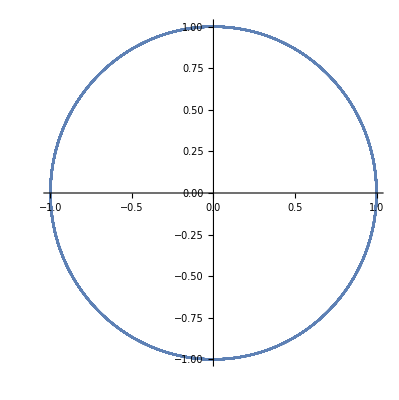

```mathematica
Clear["Global`*"]  (*Clear all variables*)
n=-1;m=1;L=1;k=-1;
ueq={u''[c]+u[c]==-m*k/(L^2*u[c]^(2+n)),u[0]==1,u'[0]==0};
ures=NDSolve[ueq,u[c],{c,0,100}];
PolarPlot[Evaluate[(1/u[c])/.ures],{c,0,100}]
```